```mathematica
SetDirectory[NotebookDirectory[]];
```

# T_scaling

## data

```mathematica
fpi=Flatten[Import["./LPA_Tscaling_mub716p5/buffer/mSigma.dat"]];
T=Flatten[Import["./LPA_Tscaling_mub716p5/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub716p5=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub716p6/buffer/mSigma.dat"]];
T=Flatten[Import["./LPA_Tscaling_mub716p6/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub716p6=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub716p65/buffer/mSigma.dat"]];
T=Flatten[Import["./LPA_Tscaling_mub716p65/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub716p65=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub716p66/buffer/mSigma.dat"]];
T=Flatten[Import["./LPA_Tscaling_mub716p66/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub716p66=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub716p6608/buffer/mSigma.dat"]];
T=Flatten[Import["./LPA_Tscaling_mub716p6608/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub716p6608=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub716p66084/buffer/mSigma.dat"]];
T=Flatten[Import["./LPA_Tscaling_mub716p66084/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub716p66084=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub716p661/buffer/mSigma.dat"]];
T=Flatten[Import["./LPA_Tscaling_mub716p661/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub716p661=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub716p66101/buffer/mSigma.dat"]];
T=Flatten[Import["./LPA_Tscaling_mub716p66101/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub716p66102=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
```

## Plot

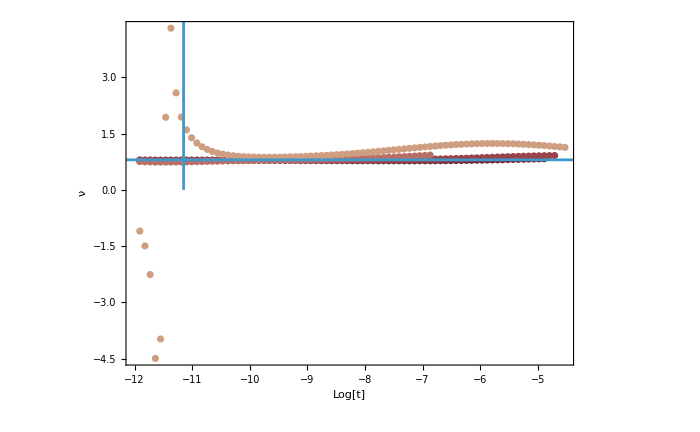

```mathematica
plotT=Show[ListPlot[{b1mub716p5,b1mub716p6,b1mub716p65,b1mub716p66(*,b1mub716p6608,b1mub716p66084,b1mub716p661,b1mub716p66102*)},
Frame->True,FrameLabel->{Style["Log[t]",25,FontFamily->"Times",Black],Style["ν",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.1}],PlotStyle->10,
(*PlotLegends->Placed[LineLegend[{"μ_B=716.5","μ_B=716.6 MeV","μ_B=716.66 MeV","μ_B=716.6608 MeV","μ_B=716.66084 MeV","μ_B=716.661 MeV","μ_B=716.66101 MeV","μ_B=350 MeV","μ_B=400 MeV","μ_B=450 MeV","μ_B=500 MeV","μ_B=550 MeV","μ_B=600 MeV","μ_B=650 MeV","μ_B=700 MeV"},LabelStyle->16],{0.23,0.7}],*)
PlotRange->All(*{{-12,-2},{0.6,0.9}}*),AxesOrigin->{-12,0.3},FrameTicksStyle->Directive[15,Black]],
ListLinePlot[{{-11.15,0},{-11.15,10}}],ListLinePlot[{{-16,0.8},{10,0.8}}],ImageSize->700,Background->None,Epilog->{Text[Style["0.8",23],{-3,0.85}]}]
```

```mathematica
Log[0.01/700]
```

-11.1563